## MICA: Measurement, Instrumentation, Control and Analysis

## Electrical Impedance Analysis

#### Ian Hunter, MIT 31 March 2026

#### Revisions

2021		Sep	17	Started
2023		Dec	04 	Updated to use the Digilent Discovery 3
2024		Apr	10	Updated
2025		Mar	12	Updated
			17	Added measured impedance plots for series and parallel configurations
			19	Added note on calibration
		Nov	12	Updated with replacement 1 mH inductor
2026		Mar	31	Added image of Digilent Impedance Analyzer PCB

-Graphics-

#### Keywords

Electrical Impedance, Impedance Gain, Impedance Phase, Resistor, Capacitor, Inductor, Resistance, Capacitance, Inductance, Ohms, Farads, Henrys

#### Objectives

In this Workstation we discuss electrical impedance analysis and use the Digilent Discovery 3 Impedance Analyzer to measure the electrical impedance of a variety of components.

#### Note

Note that when the Digilent Impedance Analyzer is first used via the Digilent Discovery 3 running Waveforms it is important to tell the software that the Impedance Analyzer is attached. If this is not done then incorrect impedance values will be recorded. As shown in the image below the menu above Mode: should be set to Adapter.

-Graphics-

Every time the resistor value is changed you will hear the relays on the Impedance Analyzer board click. If you do not hear this click then something is wrong.

#### Electrical Impedance Transfer Functions

Consider a system with a current input and a voltage output:

-Graphics-

The impedance transfer function is:

In the following we will refer to the magnitude (gain) and phase of the impedance transfer function. Together they allow us to generate the electrical impedance Bode plot by substitution the Laplace, s, by ⅈω  :

```mathematica
gain[z[s_]]:= √(Re[z[s]]^2+Im[s[s]]^2)
```

```mathematica
phase[z[s_]]:=ArcTan[Im[z[s]]/Re[z[s]]]
```

Note that in Mathematica (and as used below) we can use Abs[] and Arg[] to determine the gain[] and phase[] respectively. Note also that the phase is plotted in degrees rather than radians. Arg[] returns values in radians so to convert to degrees we multiply by  360/(2*Pi). In addition we show frequency in Hz rather than radians/s and so we substitute, s, by  ⅈ ω 2π .

Note: electrical impedance is measured over a range of frequencies. The question arises as to what that range should be. For example if your are measuring the electrical impedance of components of an audio system then given the human range of hearing goes from 20 Hz to 20 kHz you might cover that range (and perhaps a little more e.g., 10 Hz to 100 kHz) when measuring the electrical impedance of those components (including loud speakers).

Lets now consider some common components.

#### Ideal Resistor

-Graphics-           -Graphics-

The Ohm (Ω) is the unit of resistance. The symbol R and circuit symbol shown above are often used in reference to resistors.The image shows a 10 kΩ metal film resistor. 
Metal film resistors behave as ideal resistors up to moderately high frequencies (e.g., 1 MHz). Metal film resistors like the one shown above are commonly available in the range 1 Ω to 10 MΩ. Specialized resistors are available outside this range (e.g., 0.1 Ω power resistors). There are a few other types of resistors (e.g., wire wound, carbon film). Carbon film resistors sometimes change value in the process of soldering them in place.

The electrical impedance of an ideal resistor is:

```mathematica
"■"; z[s_]:=resR
```

For an ideal 10 kΩ resistor, the impedance Bode plot is:

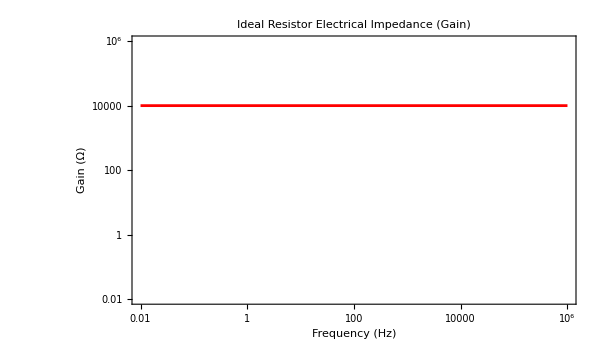

```mathematica
"■"; resR=10^4; (* 10 kΩ *)
Show[
LogLogPlot[Abs[z[ⅈ ω 2π]],{ω,0.01,10^6},PlotRange->{All,{0.01,10^6}},Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Gain (Ω)"},PlotLabel->"Ideal Resistor Electrical Impedance (Gain)", PerformanceGoal->"Quality",AspectRatio->0.6,ImageSize->600]]
```

Note that the slope of this plot is 0 and the value of the resistor is the impedance gain which is 10^4Ω = 10 kΩ .

We can also look at the phase part of the impedance transfer function:

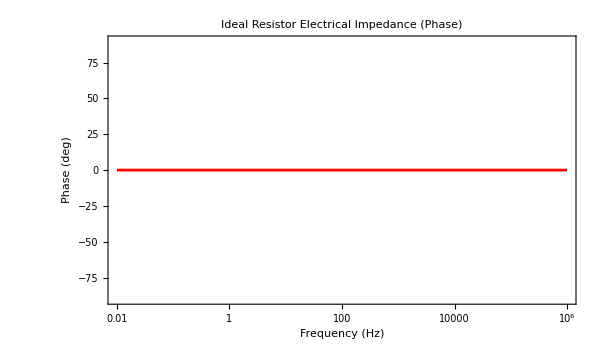

```mathematica
"■"; Show[
LogLinearPlot[360/(2*Pi)Arg[z[ⅈ ω 2π]],{ω,0.01,10^6},PlotRange->{All,{-90,90}},Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Phase (deg)"},PlotLabel->"Ideal Resistor Electrical Impedance (Phase)", PerformanceGoal->"Quality",AspectRatio->0.6,ImageSize->600]]
```

Notice that the phase of an ideal resistor is 0 deg.
Therefor for an ideal resistor the impedance Bode plot gain has a slope of 0 and a phase of 0 deg.
An ideal resistor cannot store electrical energy.

#### Real Resistor

We now will measure the impedance of a real 10 kΩ metal film resistor using the Digilent Discovery 3 fitted with the Digilent Impedance module. Make sure that the component under test (the 10 kΩ resistor here) is inserted fully in to the Digilent Impedance Module component clamps. Set up the parameters of the impedance sweep as shown in the image below:

-Graphics-

Note that the behavior of this 10 kΩ metal film resistor is close to that of an ideal 10 kΩ resistor.

-Graphics-

#### Ideal Capacitor

-Graphics-

The Farad (F) is the unit of capacitance. The symbol C and circuit symbol shown above are often used in reference to capacitors. The image shows a 680 nF capacitor. There are many types of capacitors (e.g., ceramic, silver mica, polycarbonate, polystyrene, tantalum). Tantalum capacitors only behave as ideal capacitors over a narrow range of frequencies and are usually used for “bypassing” power supply voltage fluctuations on printed circuit boards (PCBs). Silver mica capacitors are amazing and behave like pure capacitors over a wide range of frequencies but they are very expensive.
Depending on the type of material used in the capacitor construction capacitors are commonly available from 1 pF to 100 μF. Low voltage super capacitors are readily available up 3000 F (size of a beverage can).

The electrical impedance of an ideal capacitor is:

```mathematica
"■"; z[s_]:=1/(capC s)
```

For an ideal 1 nF capacitor, the impedance Bode plot is:

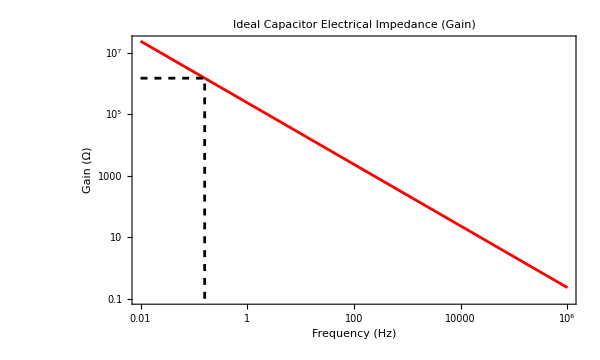

```mathematica
"■"; capC=680 10^-9; (* 680 nF *)
Show[
LogLogPlot[Abs[z[ⅈ ω 2π]],{ω,0.01,10^6},PlotRange->All,Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Gain (Ω)"},PlotLabel->"Ideal Capacitor Electrical Impedance (Gain)", PerformanceGoal->"Quality",AspectRatio->0.6,ImageSize->600],
ListLogLogPlot[{{0.01,Abs[z[ⅈ 1]]},{1/(2π) ,Abs[z[ⅈ 1]]},{1/(2π) ,0.1}},Joined->True,PlotStyle->{Black,Dashed}]]
```

Note that the slope of this plot is -1 on these Log Log axes.
Given the impedance gain plot we can deduce the value of the capacitor by evaluating z[s] at s = 1 (i.e. 1 rad/s = 1/(2π)Hz = 0.159155 Hz) and taking the reciprocal. The dashed lines show that at a frequency of 1 rad/s (i.e., 1/(2π)Hz) the impedance is :

```mathematica
"■"; z[1.0]
```

1.47059×10^6

The reciprocal of this is:

```mathematica
"■"; 1.0/z[1.0]
```

6.8×10^-7

which corresponds to a capacitance of 680 nF.

We can also look at the phase part of the impedance transfer function:

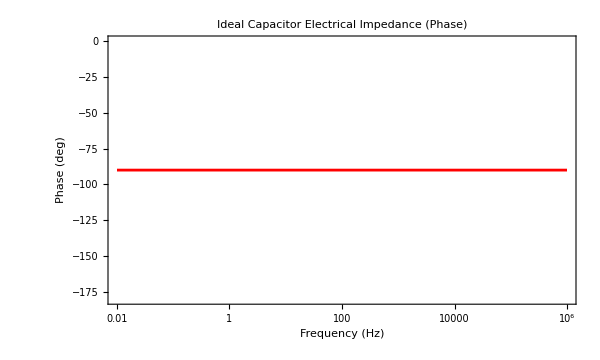

```mathematica
"■"; Show[
LogLinearPlot[360/(2*Pi)Arg[z[ⅈ ω 2π]],{ω,0.01,10^6},PlotRange->{All,{-180,0}},Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Phase (deg)"},PlotLabel->"Ideal Capacitor Electrical Impedance (Phase)", PerformanceGoal->"Quality",AspectRatio->0.6,ImageSize->600]]
```

Notice that the phase of an ideal capacitor is -90 deg.
Therefor for a capacitor the impedance Bode plot gain has a slope of -1 and the phase is -90 deg.
An ideal capacitor stores energy given by  0.5 CV^2 (where V is voltage)

#### Real Capacitor

Use the Digilent Discovery Impedance Analyzer to measure the impedance of the 680 nF capacitor supplied.  Set the Impedance Analyzer parameters as shown in the image below.

-Graphics-

Notice that the capacitor behaves like an ideal capacitor up to around 100 kHz.  At higher frequencies it will depart from this near ideal behavior.
-Graphics-

You can use the DIgilent Waveforms Impedance Analyzer to give an estimate of how well a component acts like a capacitor as a function of frequency. Set up the Waveform options as shown below (note in particular that the Capacitance button has been selected:

-Graphics-

Note that this 680 nF capacitor behaves as an ideal 680 nF capacitor from 10 Hz to 100 kHz. It would therefore be suitable for use in an audio system circuit. It starts to depart from the ideal behavior above 100 kHz.
-Graphics-

#### Ideal Inductor

-Graphics-

The Henry (H) is the unit of inductance. The symbol L and circuit symbol shown above are often used in reference to inductors. The image shows a 1 mH inductor with a ferrite core.

The electrical impedance of an ideal inductor is:

```mathematica
"■"; z[s_]:=indL s
```

For an ideal 1 mH inductor, the impedance Bode plot is:

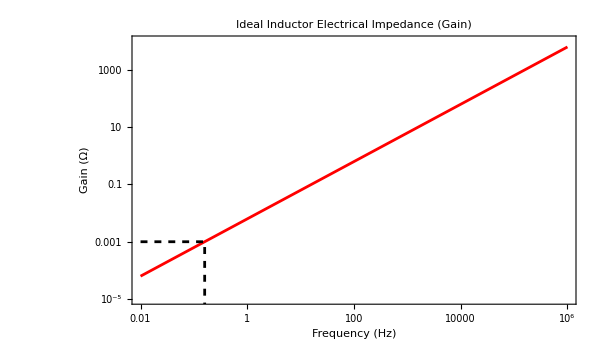

```mathematica
"■"; indL=1 10^-3; (* 1 mH *)
Show[
LogLogPlot[Abs[z[ⅈ ω 2π]],{ω,0.01, 10^6},PlotRange->{All,{10^-5,10^4}},Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Gain (Ω)"},PlotLabel->"Ideal Inductor Electrical Impedance (Gain)", PerformanceGoal->"Quality",AspectRatio->0.6,ImageSize->600],
ListLogLogPlot[{{0.01,Abs[z[ⅈ 1]]},{1/(2π) ,Abs[z[ⅈ 1]]},{1/(2π) ,1 10^-6}},Joined->True,PlotStyle->{Black,Dashed}]]
```

Note that the slope of this plot is 1 on these Log Log axes.
Given the impedance gain plot we can deduce the value of the inductor by evaluating z[s] at s = 1 (i.e. 1 rad/s = 1/(2π)Hz = 0.159155 Hz). The dashed lines show that at a frequency of 1 rad/s (i.e., 1/(2π)Hz) the impedance is 1 mΩ. This corresponds to an inductance of 1 mH.

```mathematica
N[Abs[z[ⅈ 1]]]
```

0.001

We can also look at the phase part of the impedance transfer function:

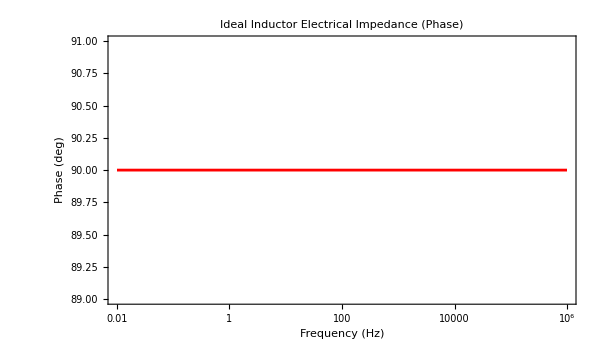

```mathematica
"■"; Show[
LogLinearPlot[360/(2*Pi)Arg[z[ⅈ ω 2π]],{ω,0.01,10^6},PlotRange->{All,{180,0}},Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Phase (deg)"},PlotLabel->"Ideal Inductor Electrical Impedance (Phase)", PerformanceGoal->"Quality",AspectRatio->0.6,ImageSize->600]]
```

Notice that the phase of an ideal inductor is 90 deg.
Therefor for an inductor the impedance Bode plot gain has a slope of +1 and a phase of +90 deg.
An ideal inductor stores energy given by  0.5 L I^2 (where I is current).

#### Real Inductor

Use the Digilent Discovery Impedance Analyzer to measure the impedance of the 1 mH inductor supplied.  Set the Impedance Analyzer parameters as shown in the image below.

-Graphics-

You will note that the measured impedance behaves like a resistor at low frequencies and like an inductor at high frequencies. This is typical of real inductors.
-Graphics-

#### Series RL (R + L)

-Graphics-

Lets consider a resistor (R) and an inductor (L) in series. In practice inductors rarely act like their ideal versions but rather often behave like they are in series with a resistor. The electrical impedance of a circuit consisting of R and L components in series is simply given by the sum of the individual component impedance transfer functions. So for the circuit above we get:

```mathematica
"■"; z[s_]:=resR + indL s ;
```

If we set the resistance and inductance to:

```mathematica
"■"; resR=2 ;   indL=1 10^-3;
```

We get an electrical impedance Bode plot of:

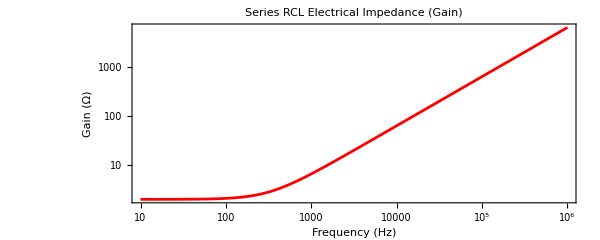

```mathematica
"■"; Show[LogLogPlot[Abs[z[ⅈ ω 2π]],{ω,10,10^6},PlotRange->All,Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Gain (Ω)"},PlotLabel->"Series RCL Electrical Impedance (Gain)", PerformanceGoal->"Quality",AspectRatio->0.4,ImageSize->600]]
```

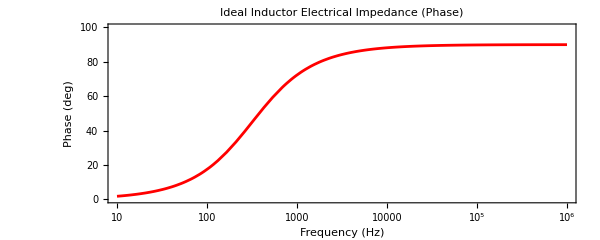

```mathematica
"■"; Show[LogLinearPlot[360/(2*Pi)Arg[z[ⅈ ω 2π]],{ω,10,10^6},PlotRange->{All,{0,100}},Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Phase (deg)"},PlotLabel->"Ideal Inductor Electrical Impedance (Phase)", PerformanceGoal->"Quality",AspectRatio->0.4,ImageSize->600]]
```

Notice that at low frequencies (10 to 100 Hz) the LR circuit behaves as a resistor (gain slope of 0 and phase of 0 deg), then at higher frequencies (10 kHz to 1 MHz) the LR circuit behaves like an inductor (gain slope of +1 and phase of +90 deg).

Compare this simulation with the measurements made on the real 1 mH inductor.

#### Series RCL (R + C + L)

-Graphics-

Lets consider a resistor (R), a capacitor (C) and an inductor (L) all in series. The electrical impedance of a circuit consisting of R, C, and L components in series is simply given by the sum of the individual component impedance transfer functions. So for the circuit above we get:

```mathematica
"■"; z[s_]:=resR + 1/(capC s)+ indL s ;
```

If we set the resistance, capacitance and inductance to:

```mathematica
"■"; resR=1 ;   capC=680 10^-9;  indL= 10^-3;
```

We get an electrical impedance Bode plot of:

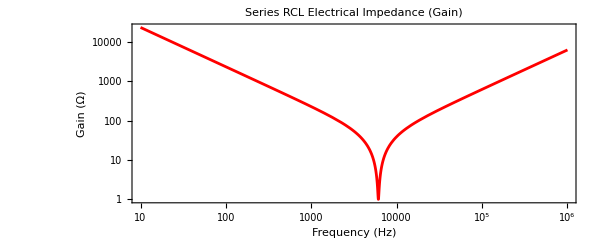

```mathematica
"■"; Show[LogLogPlot[Abs[z[ⅈ ω 2π]],{ω,10,10^6},PlotRange->All,Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Gain (Ω)"},PlotLabel->"Series RCL Electrical Impedance (Gain)", PerformanceGoal->"Quality",AspectRatio->0.4,ImageSize->600]]
```

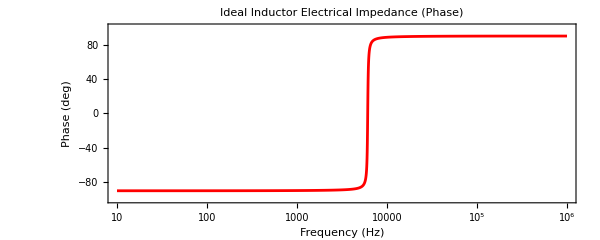

```mathematica
"■"; Show[LogLinearPlot[360/(2*Pi)Arg[z[ⅈ ω 2π]],{ω,10,10^6},PlotRange->{All,{-100,100}},Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Phase (deg)"},PlotLabel->"Ideal Inductor Electrical Impedance (Phase)", PerformanceGoal->"Quality",AspectRatio->0.4,ImageSize->600]]
```

Notice that at low frequencies (10 Hz to 1 kHz) the LCR circuit behaves as a capacitor (gain slope of -1 and phase of -90 deg) and at higher frequencies (10 kHz to 1 MHz) the LCR circuit behaves like an inductor (gain slope of +1 and phase of +90 deg).

If we can lower the series resistance even further we can get a sharper dip in the impedance gain:

```mathematica
"■"; z[s_]:=resR + 1/(capC s)+ indL s ;
```

```mathematica
"■"; resR=0.1 ;   capC=680 10^-9;  indL= 10^-3;
```

We get an electrical impedance Bode plot of:

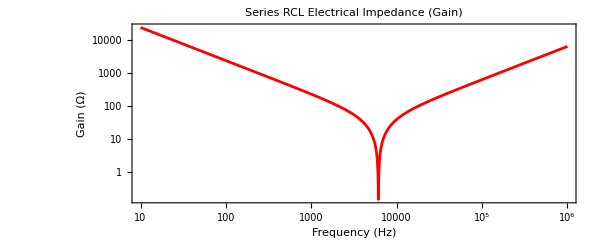

```mathematica
"■"; Show[LogLogPlot[Abs[z[ⅈ ω 2π]],{ω,10,10^6},PlotRange->All,Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Gain (Ω)"},PlotLabel->"Series RCL Electrical Impedance (Gain)", PerformanceGoal->"Quality",AspectRatio->0.4,ImageSize->600]]
```

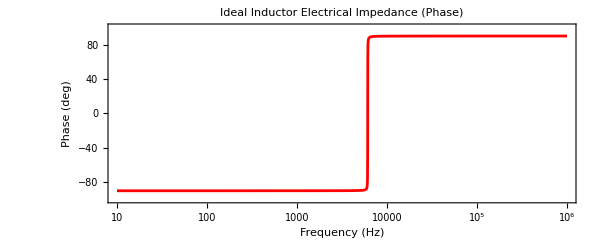

```mathematica
"■"; Show[LogLinearPlot[360/(2*Pi)Arg[z[ⅈ ω 2π]],{ω,10,10^6},PlotRange->{All,{-100,100}},Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Phase (deg)"},PlotLabel->"Ideal Inductor Electrical Impedance (Phase)", PerformanceGoal->"Quality",AspectRatio->0.4,ImageSize->600]]
```

If we have a variable capacitor (such as are used to tune analog AM radios) then we can sweep the notch across frequencies:

```mathematica
"■"; Manipulate[
z[s_]:=resR + 1/(capC s)+ indL s ;
resR=0.1 ; indL= 10^-3; 
Show[LogLogPlot[Abs[z[ⅈ ω 2π]],{ω,10,10^6},PlotRange->{{10,1000000},{0.1,100000}},Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Gain (Ω)"},PlotLabel->"Series RCL Electrical Impedance (Gain)", PerformanceGoal->"Quality",AspectRatio->0.4,ImageSize->600]],
{{capC,100. 10^-8,"Capacitance"},25. 10^-8,25. 10^-6,1. 10^-8,Appearance->"Labeled"}]
```

Use the supplied breadboard and patch cables to connect the 650 nF capacitor and 1 mH inductor in series and measure the impedance Gain and Phase over the frequency range and other settings (note the 501 Steps required to see clearly the central dip in impedance) shown below:

-Graphics-

#### Parallel RCL (R || C || L)

Here we have a resistor (R),  a capacitor (C) and an inductor (L) all in parallel. The electrical impedance of a circuit consisting of L or R or C components in parallel is simply given by the reciprocal of the sum of the reciprocals of the individual impedance transfer functions. So for the circuit above we get:

```mathematica
"■"; z[s_]:=( resR^-1+(1/(capC s))^-1+ (indL s)^-1)^-1 ;
```

If we set the resistance, capacitance and inductance to:

```mathematica
"■"; resR=10^4 ;   capC=680 10^-9;  indL=10^-3;
```

We get an electrical impedance Bode plot of:

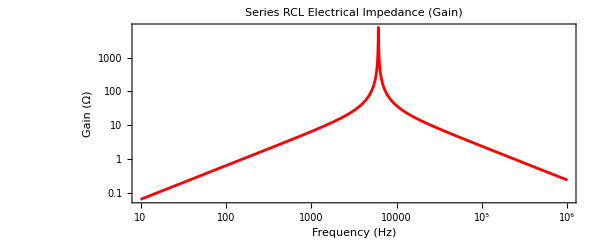

```mathematica
"■"; Show[LogLogPlot[Abs[z[ⅈ ω 2π]],{ω,10,10^6},PlotRange->All,Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Gain (Ω)"},PlotLabel->"Series RCL Electrical Impedance (Gain)", PerformanceGoal->"Quality",AspectRatio->0.4,ImageSize->600]]
```

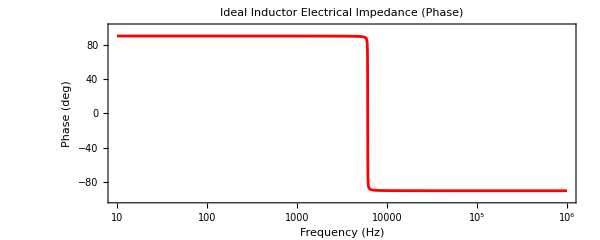

```mathematica
"■"; Show[LogLinearPlot[360/(2*Pi)Arg[z[ⅈ ω 2π]],{ω,10,10^6},PlotRange->{All,{-100,100}},Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Phase (deg)"},PlotLabel->"Ideal Inductor Electrical Impedance (Phase)", PerformanceGoal->"Quality",AspectRatio->0.4,ImageSize->600]]
```

Notice that at low frequencies (10 Hz to 1 kHz) the LCR circuit behaves as an inductor (gain slope of +1 and phase of +90 deg) and at higher frequencies (10 kHz to 1 MHz) the circuit behaves like an capacitor (gain slope of -1 and phase of -90 deg).

Use the supplied breadboard and patch cables to connect the 10 kΩ resistor, 650 nF capacitor and 1 mH inductor in parallel and measure the impedance Gain and Phase over the frequency range and other settings (note the 501 Steps required to see clearly the central peak in impedance) shown below:

-Graphics-
-Graphics-
flipped

Note that the impedance gain peak and the abrupt phase change at around 6 kHz occurs in both the measured and theoretical responses.
However notice that at low frequencies there is a significant difference between the theoretical and measured plots. It is likely that the non-ideal behavior of the inductor noted earlier at low frequencies contributed to the differences at low frequencies. Lets check this by adding a series resistor to the inductor:

```mathematica
"■"; z[s_]:=( resR1^-1+(1/(capC s))^-1+ (resR2+indL s)^-1)^-1 ;
```

If we set the resistance, capacitance and inductance to:

```mathematica
"■"; resR1=10^4 ;   resR2=2 ;   capC=680 10^-9;  indL=10^-3;
```

We get an electrical impedance Bode plot of:

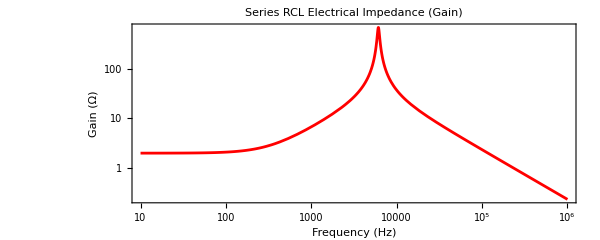

```mathematica
"■"; Show[LogLogPlot[Abs[z[ⅈ ω 2π]],{ω,10,10^6},PlotRange->All,Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Gain (Ω)"},PlotLabel->"Series RCL Electrical Impedance (Gain)", PerformanceGoal->"Quality",AspectRatio->0.4,ImageSize->600]]
```

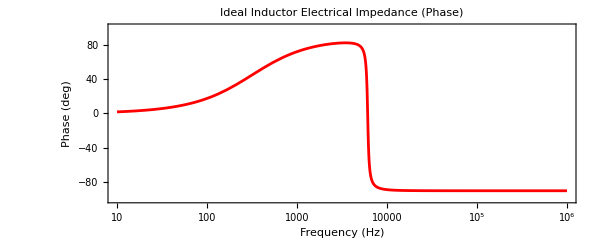

```mathematica
"■"; Show[LogLinearPlot[360/(2*Pi)Arg[z[ⅈ ω 2π]],{ω,10,10^6},PlotRange->{All,{-100,100}},Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Phase (deg)"},PlotLabel->"Ideal Inductor Electrical Impedance (Phase)", PerformanceGoal->"Quality",AspectRatio->0.4,ImageSize->600]]
```

This works!

#### Resonant Circuit (R + (C || L))

-Graphics-

Here we have a resistor in series with a capacitor and inductor in parallel. So for the circuit above we get:

```mathematica
"■"; z[s_]:=resR +( (1/(capC s))^-1+ (indL s)^-1)^-1 ;
```

If we set the resistance, capacitance and inductance to:

```mathematica
"■"; resR=10^4 ;   capC=680 10^-9;  indL=10^-3;
```

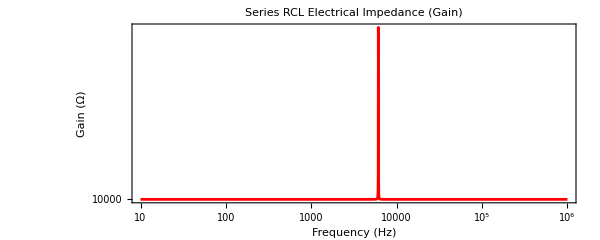

```mathematica
"■"; Show[LogLogPlot[Abs[z[ⅈ ω 2π]],{ω,10,10^6},PlotRange->All,Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Gain (Ω)"},PlotLabel->"Series RCL Electrical Impedance (Gain)", PerformanceGoal->"Quality",AspectRatio->0.4,ImageSize->600]]
```

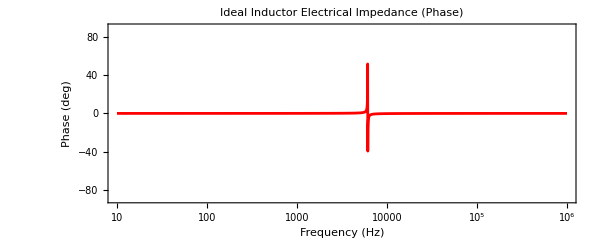

```mathematica
"■"; Show[LogLinearPlot[360/(2*Pi)Arg[z[ⅈ ω 2π]],{ω,10,10^6},PlotRange->{All,{-90,90}},Frame->True,PlotStyle->Red,LabelStyle->{12,Black},GridLines->Automatic,FrameLabel->{"Frequency (Hz)","Phase (deg)"},PlotLabel->"Ideal Inductor Electrical Impedance (Phase)", PerformanceGoal->"Quality",AspectRatio->0.4,ImageSize->600]]
```

Use the supplied breadboard and patch cables to connect the 10 kΩ resistor in series with a parallel connection of the 650 nF capacitor and 1 mH inductor as shown above and measure the impedance Gain and Phase over the frequency range and other settings (note the 2001 Steps required to see clearly the central peak in impedance) shown below:

-Graphics-
-Graphics-
couldn’t get large enough time stamp

Note that the change in impedance gain and phase is really small. This is how you can null the effect of a capacitance with an inductor in parallel with it or equivalently null the effect of an inductor by adding a capacitor in parallel with it.

#### Probe Calibration

The probes and impedance analyzer connectors have their own resistances, capacitances and sometimes inductances that change impedance readings particularly at high frequencies. For higher frequencies than 100 kHz it is important to “calibrate out” (correct for) these effects by measuring the impedance gain and phase when the impedance analyzer junctions are shorted (zero resistance calibration) and when not connected to (open circuit calibration).  All impedance analyzers including the Digilent Discovery 3 Impedance Analyzer have this capability.